```mathematica
?Template*
```

TemplateRectangular[nx,ny]
TemplateRectangular[{xmin,xmax,dx}, {ymin,ymax,dy}]

```mathematica
w=TemplateCircularHoneycombCover[15];
n=NTissueCells[w];
clr:= Hue[RandomReal[{0,1}]]; 
clrs=Table[clr, {n}];
```

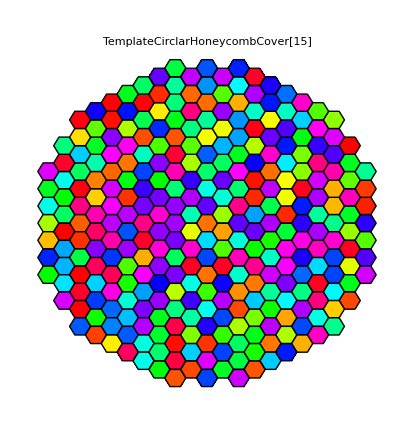

```mathematica
temp1=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateCirclarHoneycombCover[15]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp1.png", temp1, ImageSize-> 500]
```

temp1.png

```mathematica
w=TemplateCircularHoneycombCover[18, 5];
n=NTissueCells[w];
clr:= Hue[RandomReal[{0,1}]]; 
clrs=Table[clr, {n}];
```

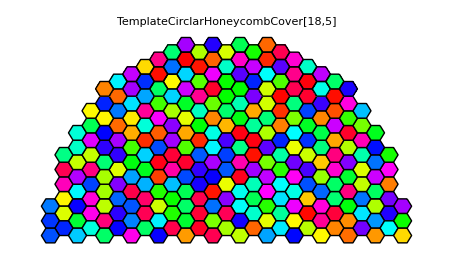

```mathematica
temp2=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateCirclarHoneycombCover[18,5]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp2.png", temp2, ImageSize-> 500]
```

temp2.png

```mathematica
w=TemplateHoneycombCover[18, 10];
n=NTissueCells[w];
rv:= RandomReal[{.3, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

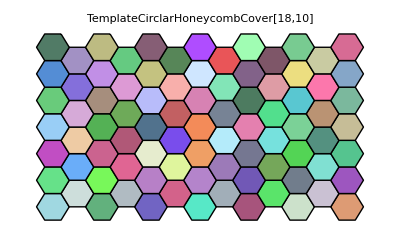

```mathematica
temp3=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateCirclarHoneycombCover[18,10]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp3.png", temp3, ImageSize-> 500]
```

temp3.png

```mathematica
w=TemplateRandom[200 ,
{{0,0}, {10, -3}, {15, 5}, {13, 12}, {-1, 10}}
];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

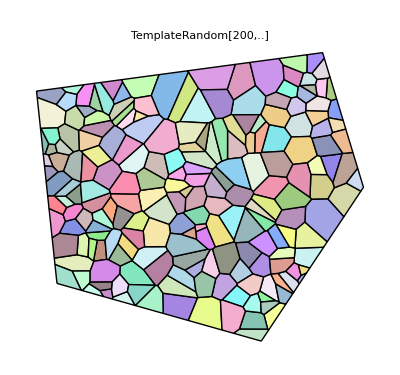

```mathematica
temp4=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateRandom[200,..]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp4.png", temp4, ImageSize-> 500]
```

temp4.png

```mathematica
w=TemplateRandomCircularGrid[200, 100];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

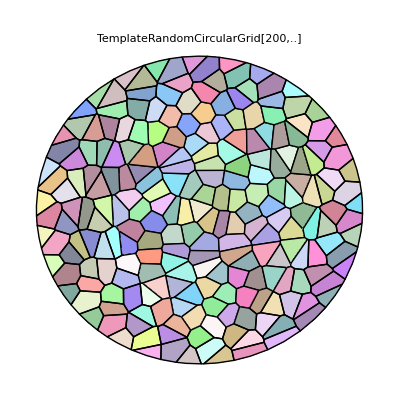

```mathematica
temp5=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateRandomCircularGrid[200,..]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp5.png", temp5, ImageSize-> 500]
```

temp5.png

```mathematica
w=TemplateRandomSemicircularGrid[200, 100, 15];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

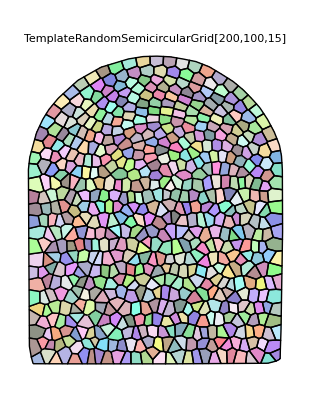

```mathematica
temp6=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateRandomSemicircularGrid[200,100,15]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp6.png", temp6, ImageSize-> 800]
```

temp6.png

```mathematica
w=TemplateRandomSquareGrid[200,{0,0}, {100, 100}];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

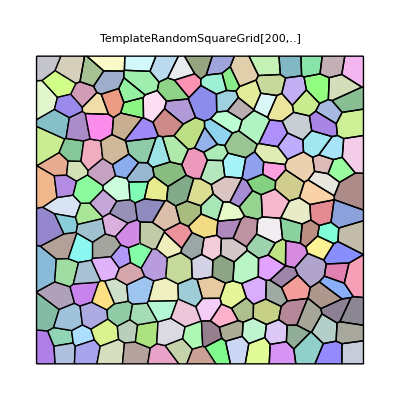

```mathematica
temp7=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateRandomSquareGrid[200,..]", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp7.png", temp7, ImageSize-> 800]
```

temp7.png

```mathematica
"TemplateRectangular[{xmin,xmax,dx}, {ymin,ymax,dy}]"
```

```mathematica
"TemplateRectangular[{xmin,xmax,dx}, {ymin,ymax,dy}]"
```

```mathematica
w=TemplateRectangular[{0, 100, 5}, {0, 100, 10}];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

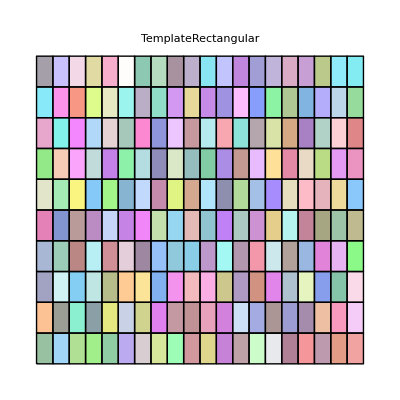

```mathematica
temp8=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateRectangular", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp8.png", temp8, ImageSize-> 800]
```

temp8.png

```mathematica
?TemplateRectangularCover
```

TemplateRectangularCover[xmax, ymax, dx, dy, offset:.5]

```mathematica
w=TemplateRectangularCover[20, 15, 5, 5];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

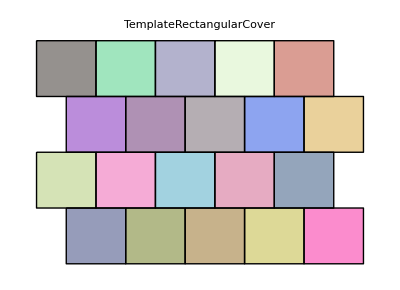

```mathematica
temp9=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateRectangularCover", BaseStyle-> {FontSize-> 18}]
```

```mathematica
Export["temp9.png", temp9, ImageSize-> 500]
```

temp9.png

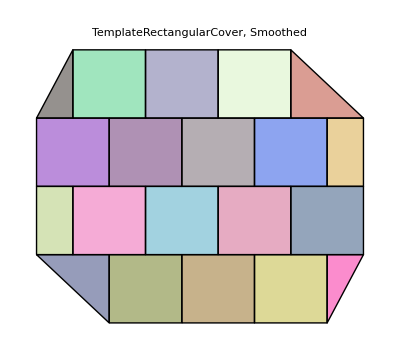

```mathematica
temp10=ShowTissue[SmootheCells[w], "CellStyle"-> clrs, PlotLabel-> "TemplateRectangularCover, Smoothed", BaseStyle-> {FontSize-> 18}]
```

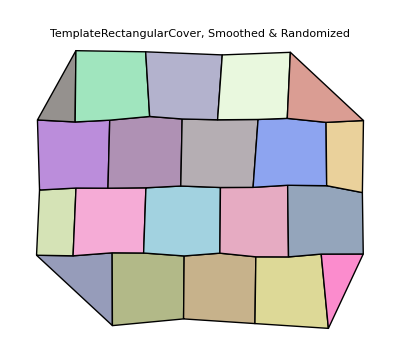

```mathematica
temp11=ShowTissue[RandomizeTemplate[SmootheCells[w],.1], "CellStyle"-> clrs, PlotLabel-> "TemplateRectangularCover, Smoothed & Randomized", BaseStyle-> {FontSize-> 12}]
```

```mathematica
Export["temp10.png", temp10, ImageSize-> 500]
```

temp10.png

```mathematica
Export["temp11.png", temp11, ImageSize-> 500]
```

templ1.png

```mathematica
w=TemplateCircularHoneycombCover[12, 5];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

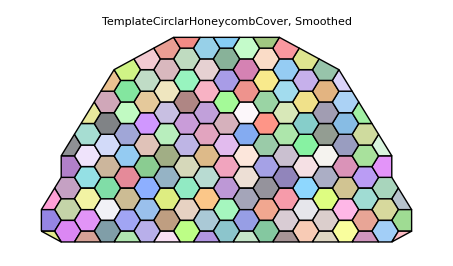

```mathematica
temp12=ShowTissue[SmootheCells[w], "CellStyle"-> clrs, PlotLabel-> "TemplateCirclarHoneycombCover, Smoothed", BaseStyle-> {FontSize-> 12}]
```

```mathematica
Export["temp12.png", temp12, ImageSize-> 500]
```

temp12.png

```mathematica
w=TemplateCircularHoneycombCover[10, 5];
n=NTissueCells[w];
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
clrs=Table[clr, {n}];
```

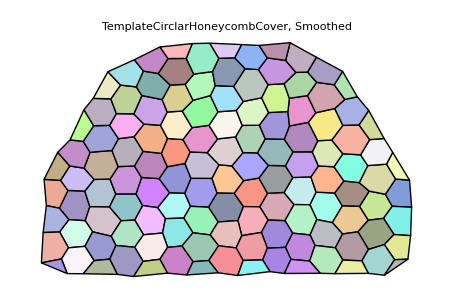

```mathematica
temp13=ShowTissue[RandomizeTemplate[SmootheCells[w], .2], "CellStyle"-> clrs, PlotLabel-> "TemplateCirclarHoneycombCover, Smoothed, Randomized", BaseStyle-> {FontSize-> 12}]
```

```mathematica
Export["temp13.png", temp13, ImageSize-> 500]
```

temp13.png

```mathematica
w=TemplateCircularHoneycombCover[10];
w=SmootheCells[w]; 
w=RandomizeTemplate[w, .2]; 
rv:= RandomReal[{.5, 1}]; 
clr:= RGBColor[rv, rv, rv];  
n=NTissueCells[w];
clrs=Table[clr, {n}];
```

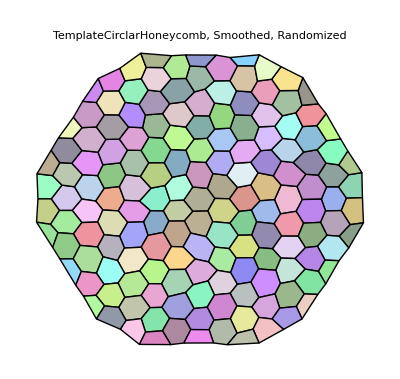

```mathematica
temp14=ShowTissue[w, "CellStyle"-> clrs, PlotLabel-> "TemplateCirclarHoneycomb, Smoothed, Randomized", BaseStyle-> {FontSize-> 12}]
```

```mathematica
Export["temp14.png", temp14, ImageSize-> 500]
```

temp14.png